```mathematica
G := SetPrecision[6.674*10^(-8), 80] (*en cgs*)
c := SetPrecision[2.998*10^(10), 80](*en cgs*)
ti :=SetPrecision[ 1.48*10^(12), 80](*s*)
ρt :=SetPrecision[ 100, 80] (*cgs *)
```

```mathematica
ηb :=2.19*10^4
```

```mathematica
func[ρcrit = √((3*c^2)/(8*π*G*ab^2*ηb^2))x_] := SetPrecision[1/2*1/((1+x^2)^(1/2))*(ArcSinh[x]+x √(1+x^2))-ti/ηb, 80]
```

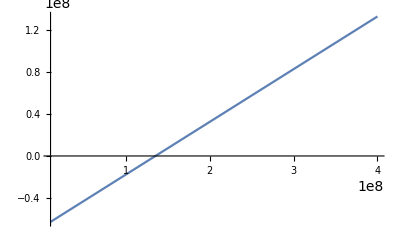

```mathematica
Plot[func[x], {x, 10^7, 4*10^8}]
```

```mathematica
FindRoot[func[x], {x, 1.5*10^8}]
```

{x→1.3516×10^8}

```mathematica
xi =1.3515981735159802*^8
```

1.3516×10^8

```mathematica
ηi = xi*ηb
```

2.96×10^12

```mathematica
ab =1/(1+xi^2)^(1/2)
```

7.39865×10^-9

```mathematica
ρcrit = √((3*c^2)/(8*π*G*ab^2*ηb^2))
```

2.47447×10^17

```mathematica
Clear[ηb]
```

```mathematica
ηb :=4.93*10^8
```

```mathematica
func[x_] := SetPrecision[1/2*1/((1+x^2)^(1/2))*(ArcSinh[x]+x √(1+x^2))-ti/ηb, 80]
```

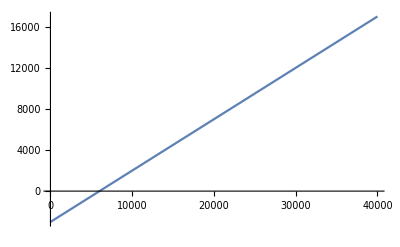

```mathematica
Plot[func[x], {x, 10^1, 4*10^4}]
```

```mathematica
FindRoot[func[x], {x, 6000}]
```

{x→6004.06}

```mathematica
xi =6004.0552306330055
```

6004.06

```mathematica
ηi = xi*ηb
```

2.96×10^12

```mathematica
ab =1/(1+xi^2)^(1/2)
```

0.000166554

```mathematica
ρcrit = √((3*c^2)/(8*π*G*ab^2*ηb^2))
```

4.88289×10^8

```mathematica
Clear[ηb]
```

```mathematica
ηb :=2.47*10^(-15)
```

```mathematica
func[x_] := SetPrecision[1/2*1/((1+x^2)^(1/2))*(ArcSinh[x]+x √(1+x^2))-ti/ηb, 80]
```

```mathematica
Plot[func[x], {x, 10^25, 4*10^27}]
```

```mathematica
ρcrit = √((3*c^2)/(8*π*G*ab^2*ηb^2))
```

```mathematica
FindRoot[func[x], {x, 1*10^(27)}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→1.19838×10^27}

```mathematica
xi =1.1983805668016192*^27
```

1.19838×10^27

```mathematica
ηi = xi*ηb
```

2.96×10^12

```mathematica
ab =1/(1+xi^2)^(1/2)
```

8.34459×10^-28

```mathematica
ρcrit = √((3*c^2)/(8*π*G*ab^2*ηb^2))
```

1.94526×10^55